/Users/ant/Sites/JumpStartIM/assets/images/functions

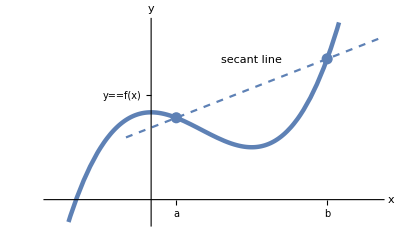

{diffq1.svg,diffq1.pdf}

```mathematica
SetDirectory[NotebookDirectory[]]
f[x_]:=x^3-3x^2+10
a=0.5;b=3.5;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,-2,4.5},PlotStyle->{Thickness[0.008]},Ticks->{{{b,HoldForm[b]},{a,HoldForm[a]}},{{f[0]+2,HoldForm[y==f[x]]}}}],
ListPlot[{{a,f[a]},{b,f[b]}},PlotStyle->PointSize[0.02]],
Plot[m(x-a)+f[a],{x,-1/2,10},PlotStyle->Dashed],
(*Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],*)
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y},Epilog->{
Style[Text["secant line",{2,16}],16]}
]
Export[{"diffq1.svg","diffq1.pdf"},%]
```

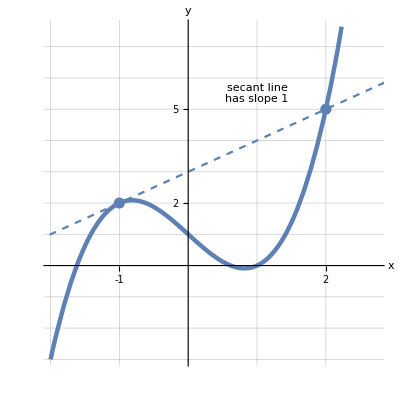

{diffq2.svg,diffq2.pdf}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=x^3-2x+1
a=-1;b=2;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,-2,2.75},PlotStyle->{Thickness[0.008]},Ticks->{{{b,b},{a,a}},{f[a],f[b]}}],
ListPlot[{{a,f[a]},{b,f[b]}},PlotStyle->PointSize[0.02]],
Plot[m(x-a)+f[a],{x,-4,10},PlotStyle->Dashed],
(*Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],*)
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y},Epilog->{
Style[Text["secant line\nhas slope 1",{1,5.5}],16]},GridLines->{Range[-3,3],Range[-10,10]},AspectRatio->1
]
Export[{"diffq2.svg","diffq2.pdf"},%]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

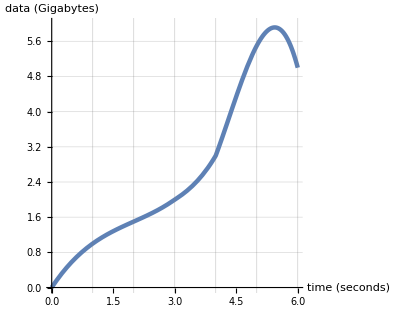

{diffqdata1.svg,diffqdata1.pdf}

```mathematica
SetDirectory[NotebookDirectory[]];
data={{0,0},{1,1},{2,1.5},{3,2},{4,3},{5,5.5},{6,5}};
f=Interpolation[data]
a=-1;b=2;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,0,6},PlotStyle->{Thickness[0.008]}],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{"time\n(seconds)","data\n(Gigabytes)"},
(*Epilog->{
Style[Text["secant line\nhas slope 1",{1,5.5}],16]},*)GridLines->{Range[-10,10],Range[-10,10,0.5]},AspectRatio->0.8,PlotRange->{{0,6},{0,6}}
]
Export[{"diffqdata1.svg","diffqdata1.pdf"},%]
```

```mathematica
f[0]
```

InterpolatingFunction[{{0,0},{2,1.5},{4,3},{5,5.5},{6,5}}][0]

```mathematica
f
```

InterpolatingFunction[{{0,0},{2,1.5},{4,3},{5,5.5},{6,5}}]

```mathematica
InterpolatingFunction[data][x]
```

InterpolatingFunction[{{0,0},{2,1.5},{4,3},{5,5.5},{6,5}}][x]

```mathematica
points={{0,0},{1,1},{2,3},{3,4},{4,3},{5,0}};
ifun=Interpolation[points]
```

InterpolatingFunction[…]

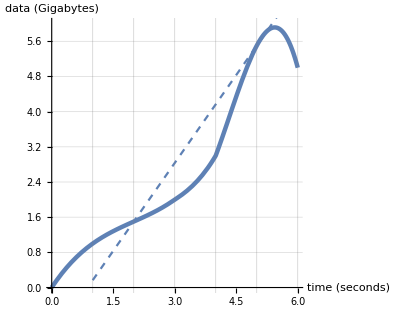

{diffqdata2.svg,diffqdata2.pdf}

```mathematica
a=2;b=5;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,0,6},PlotStyle->{Thickness[0.008]}],
Plot[m(x-a)+f[a],{x,1,10},PlotStyle->Dashed],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{"time\n(seconds)","data\n(Gigabytes)"},
(*Epilog->{
Style[Text["secant line\nhas slope 1",{1,5.5}],16]},*)GridLines->{Range[-10,10],Range[-10,10,0.5]},AspectRatio->0.8,PlotRange->{{0,6},{0,6}}
]
Export[{"diffqdata2.svg","diffqdata2.pdf"},%]
```

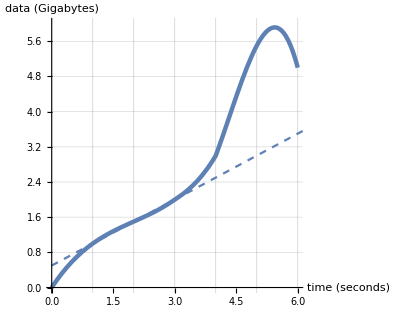

{diffqdata3.svg,diffqdata3.pdf}

```mathematica
a=2;b=3;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,0,6},PlotStyle->{Thickness[0.008]}],
Plot[m(x-a)+f[a],{x,0,10},PlotStyle->Dashed],
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{"time\n(seconds)","data\n(Gigabytes)"},
(*Epilog->{
Style[Text["secant line\nhas slope 1",{1,5.5}],16]},*)GridLines->{Range[-10,10],Range[-10,10,0.5]},AspectRatio->0.8,PlotRange->{{0,6},{0,6}}
]
Export[{"diffqdata3.svg","diffqdata3.pdf"},%]
```

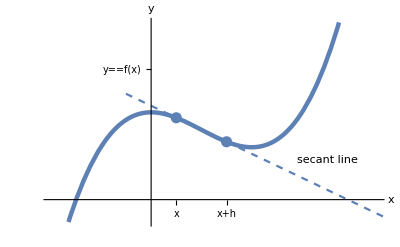

{diffqh1.svg,diffqh1.pdf}

```mathematica
Unset[f];
f[x_]:=x^3-3x^2+10
a=0.5;b=1.5;
m=(f[b]-f[a])/(b-a);
Show[
Plot[f[x],{x,-2,4.5},PlotStyle->{Thickness[0.008]},Ticks->{{{b,HoldForm[x+h]},{a,HoldForm[x]}},{{f[0]+5,HoldForm[y==f[x]]}}}],
ListPlot[{{a,f[a]},{b,f[b]}},PlotStyle->PointSize[0.02]],
Plot[m(x-a)+f[a],{x,-1/2,10},PlotStyle->Dashed],
(*Graphics[{Dashed,Line[{{3.5,0},{3.5,f[3.5]},{0,f[3.5]}}]}],*)
TicksStyle->Directive[16],
AxesStyle->Directive[14],
AxesLabel->{x,y},Epilog->{
Style[Text["secant line",{3.5,4.5}],16]}
]
Export[{"diffqh1.svg","diffqh1.pdf"},%]
```